```mathematica
Clear["Global`*"]
```

## Input

```mathematica
(* units *)
fm=5.0676896;

(* structures *)
J=0;
L=0;
s1=1/2;
s2=1/2;
Cij=-4/3;

(* masses *)
mu=0.220;
md=0.220;
ms=0.419;
mc=1.628;
mb=4.977;
mt=172.57;
mi=mc;
mj=mc;

(* GIC parameters *)
αk={0.25,0.15,0.20};
γk={1/2,√(5/2),5 √10};
b=0.18;
c=-0.253;
σ0=1.8;
s=1.55;
ϵCoul=0;
ϵcont=-0.168;
ϵtens=0.025;
ϵsoν=-0.035;
ϵsos=0.055;
μ=0.15;

(* GEM parameters *)
nmax=20;
rmin=0.10fm;
rmax=10.0fm;
```

## Spin

```mathematica
NineJSymbol[{j1_,j2_,j12_},{j3_,j4_,j34_},{j13_,j24_,J_}]:=
Module[{res,x,xmin,xmax},
If[j1<0||j2<0||j12<0||j3<0||j4<0||j34<0||j13<0||j24<0||J<0,Return[0]];
If[j1+j2<j12||Abs[j1-j2]>j12||Mod[j1+j2+j12,1]≠0,Return[0]];
If[j3+j4<j34||Abs[j3-j4]>j34||Mod[j3+j4+j34,1]≠0,Return[0]];
If[j1+j3<j13||Abs[j1-j3]>j13||Mod[j1+j3+j13,1]≠0,Return[0]];
If[j2+j4<j24||Abs[j2-j4]>j24||Mod[j2+j4+j24,1]≠0,Return[0]];
If[j12+j34<J||Abs[j12-j34]>J||Mod[j12+j34+J,1]≠0,Return[0]];
If[j13+j24<J||Abs[j13-j24]>J||Mod[j13+j24+J,1]≠0,Return[0]];
xmin=Max[Abs[j2-j34],Abs[j3-j24]];
xmax=Min[j2+j34,j3+j24];
res=Sum[(-1)^(2*x)*(2*x+1)*
SixJSymbol[{j1,j2,j12},{j34,J,x}]*SixJSymbol[{j3,j4,j34},{j2,x,j24}]*SixJSymbol[{j13,j24,J},{x,j1,j3}]
,{x,xmin,xmax}];
Return[res]]
SdS[{s1p_,s2p_,Sp_,Lp_},{s1_,s2_,S_,L_},J_]:=(S(S+1)-s1(s1+1)-s2(s2+1))/2*KroneckerDelta[{s1p,s2p,Sp,Lp},{s1,s2,S,L}]
S1L[{s1p_,s2p_,Sp_,Lp_},{s1_,s2_,S_,L_},J_]:=(-1)^(S+Lp+J)SixJSymbol[{Sp,S,1},{L,Lp,J}]*(-1)^(s1p+s2p+S+1)√((2Sp+1)(2S+1))SixJSymbol[{s1,s1p,1},{Sp,S,s2p}]*√((2s1+1)(s1+1)s1)*√((2L+1)(L+1)L)*KroneckerDelta[{s1p,s2p,Lp},{s1,s2,L}]
S2L[{s1p_,s2p_,Sp_,Lp_},{s1_,s2_,S_,L_},J_]:=(-1)^(S+Lp+J)SixJSymbol[{Sp,S,1},{L,Lp,J}]*(-1)^(s1+s2+Sp+1)√((2Sp+1)(2S+1))SixJSymbol[{s2,s2p,1},{Sp,S,s1p}] √((2s2+1)(s2+1)s2)*√((2L+1)(L+1)L)*KroneckerDelta[{s1p,s2p,Lp},{s1,s2,L}]
Ten[{s1p_,s2p_,Sp_,Lp_},{s1_,s2_,S_,L_},J_]:=
(-1)^(S+Lp+J)√((24π)/5)SixJSymbol[{Sp,S,2},{L,Lp,J}]*
√(5(2Sp+1)(2S+1))NineJSymbol[{s1p,s1,1},{s2p,s2,1},{Sp,S,2}] √((2s1+1)(s1+1)s1)√((2s2+1)(s2+1)s2)*
(-1)^Lp √((5(2Lp+1)(2L+1))/(4π))ThreeJSymbol[{Lp,0},{2,0},{L,0}]*KroneckerDelta[{s1p,s2p},{s1,s2}]
```

```mathematica
(*j-j*)
JJ={};
Do[If[Abs[jl-s2]≤J≤jl+s2,JJ=Join[JJ,{{s1,s2,jl,L}}]],{jl,Abs[L-s1],L+s1}]
JJ;
trans=Table[S=SL[[i,3]];jl=JJ[[j,3]];(-1)^(s2+L+S+jl)√((2S+1)(2jl+1))SixJSymbol[{s2,s1,S},{L,J,jl}],{j,1,Length[JJ]},{i,1,Length[SL]}];

(*S-L*)
SL={};
Do[If[Abs[S-L]≤J≤S+L,SL=Join[SL,{{s1,s2,S,L}}]],{S,Abs[s1-s2],s1+s2}]
SL
trans=Table[KroneckerDelta[f,i],{f,1,Length[SL]},{i,1,Length[SL]}]
```

{{1/2,1/2,0,0}}

{{1}}

```mathematica
OSdS=Table[SdS[SL[[f]],SL[[i]],J],{f,1,Length[SL]},{i,1,Length[SL]}];
OS1L=Table[S1L[SL[[f]],SL[[i]],J],{f,1,Length[SL]},{i,1,Length[SL]}];
OS2L=Table[S2L[SL[[f]],SL[[i]],J],{f,1,Length[SL]},{i,1,Length[SL]}];
OTen=Table[Ten[SL[[f]],SL[[i]],J],{f,1,Length[SL]},{i,1,Length[SL]}];
OCen=Table[KroneckerDelta[SL[[f]],SL[[i]]],{f,1,Length[SL]},{i,1,Length[SL]}];

OSdS=Transpose[trans].OSdS.trans//Simplify
OS1L=Transpose[trans].OS1L.trans//Simplify
OS2L=Transpose[trans].OS2L.trans//Simplify
OTen=Transpose[trans].OTen.trans//Simplify
OCen=Transpose[trans].OCen.trans//Simplify
```

SixJSymbol::tri: SixJSymbol[{0,0,1},{0,0,0}] is not triangular.

SixJSymbol::tri: SixJSymbol[{1/2,1/2,1},{0,0,1/2}] is not triangular.

SixJSymbol::tri: SixJSymbol[{0,0,1},{0,0,0}] is not triangular.

SixJSymbol::tri: SixJSymbol[{1/2,1/2,1},{0,0,1/2}] is not triangular.

SixJSymbol::tri: SixJSymbol[{0,0,2},{0,0,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{0,0}] is not triangular.

{{-3/4}}

{{0}}

{{0}}

{{0}}

{{1}}

## GEM

```mathematica
(* Gaussian basis *)
ν[n_]:=1/rmin^2(rmax/rmin)^((2-2n)/(nmax-1))
Rnlp[p_,n_,l_]:=(-ⅈ)^l 2^(-l/2-1/4)ν[n]^(-l/2-3/4)√(1/Gamma[l+3/2])p^l Exp[-p^2/(4 ν[n])]
Rnlr[r_,n_,l_]:=2^(l/2+5/4) ν[n]^(l/2+3/4)√(1/Gamma[l+3/2])r^l Exp[-r^2 ν[n]]
```

{{0.-0.567656 (5.62837 ⅇ^(-9.25199 r^2)+0.419118 ⅇ^(-1.98379 r^2)+0.0300688 ⅇ^(-0.24366 r^2))-1.33333 ((0.25 Erf[0.493619 r])/r+(0.15 Erf[1.40847 r])/r+(0.2 Erf[3.04171 r])/r)+(0.173475 ⅇ^(-0.15 r) (5.45901 ⅇ^(0.15 r) r+0.180105 (0.15-19.2151 r) Erfc[0.161311 (0.15-19.2151 r)]-0.18 ⅇ^(0.0375 (0.0156127+8 r)) (0.15+19.2151 r) Erfc[0.161311 (0.15+19.2151 r)]))/r}}

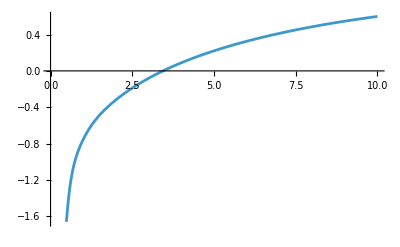

```mathematica
(* Hamiltonium *)
T=(√(mi^2+p^2)+√(mj^2+p^2))*OCen;
βij=(1+p^2/((p^2+mi^2)^(1/2)(p^2+mj^2)^(1/2)))*OCen;
δij=(mi*mj)/((p^2+mi^2)^(1/2)(p^2+mj^2)^(1/2))*OCen;
δii=(mi*mi)/((p^2+mi^2)^(1/2)(p^2+mi^2)^(1/2))*OCen;
δjj=(mj*mj)/((p^2+mj^2)^(1/2)(p^2+mj^2)^(1/2))*OCen;
σij=√(σ0^2(1/2+1/2((4mi*mj)/(mi+mj)^2)^4)+s^2((2mi*mj)/(mi+mj))^2);
σkij=Table[(γk[[k]]*σij)/(√(γk[[k]]^2+σij^2)),{k,1,3}];
VCoul=Cij*Sum[αk[[k]]/r Erf[σkij[[k]]*r],{k,1,3}]*OCen;
Vconf=(-1/(16r*μ*σij^3)3 Cij*Exp[-r*μ]*σij (4Exp[r*μ]*r(b+c*μ) σij^2+b*Exp[μ^2/(4 σij^2)](μ-2 r*σij^2) Erfc[(μ-2 r*σij^2)/(2σij)]-b*Exp[1/4 μ (8 r+μ/σij^2)](μ+2 r*σij^2) Erfc[(μ+2 r*σij^2)/(2 σij)]))*OCen;
Vcont=(32OSdS)/(9mi*mj √π)Sum[αk[[k]] σkij[[k]]^3 Exp[-σkij[[k]]^2 r^2],{k,1,3}];
Vtens=OTen/(3mi*mj)*(1/r D[VCoul,{r,1}]-D[VCoul,{r,2}]);
Vsoνi=1/r D[VCoul,{r,1}](OS1L/(2 mi^2));
Vsoνj=1/r D[VCoul,{r,1}](-OS2L/(2 mj^2));
Vsoνij=1/r D[VCoul,{r,1}](-(OS1L-OS2L)/(2mi*mj));
Vsosi=1/r D[Vconf,{r,1}](-OS1L/(2 mi^2));
Vsosj=1/r D[Vconf,{r,1}](OS2L/(2 mj^2));
V=βij^(1/2+ϵCoul)*VCoul*βij^(1/2+ϵCoul)+Vconf+δij^(1/2+ϵcont)*Vcont*δij^(1/2+ϵcont)+δij^(1/2+ϵtens)*Vtens*δij^(1/2+ϵtens)+δii^(1/2+ϵsoν)*Vsoνi*δii^(1/2+ϵsoν)+δjj^(1/2+ϵsoν)*Vsoνj*δjj^(1/2+ϵsoν)+δij^(1/2+ϵsoν)*Vsoνij*δij^(1/2+ϵsoν)+δii^(1/2+ϵsos)*Vsosi*δii^(1/2+ϵsos)+δjj^(1/2+ϵsos)*Vsosj*δjj^(1/2+ϵsos)/.{p->0}
Plot[V,{r,0,10}]
```

```mathematica
(* Matrix elements *)
NSL={};
Do[NSL=Join[NSL,{{n,SL[[i,4]],i}}],{i,1,Length[SL]},{n,1,nmax}];
NSL
mT=ParallelTable[
{nf,lf,of}=NSL[[f]];
{ni,li,oi}=NSL[[i]];
NIntegrate[Conjugate[Rnlp[p,nf,lf]]*T[[of,oi]]*Rnlp[p,ni,li]*p^2,{p,0,Infinity}],{f,1,Length[NSL]},{i,1,Length[NSL]}];
mβijCoul=ParallelTable[
{nf,lf,of}=NSL[[f]];
{ni,li,oi}=NSL[[i]];
NIntegrate[Conjugate[Rnlp[p,nf,lf]]*(βij^(1/2+ϵCoul))[[of,oi]]*Rnlp[p,ni,li]*p^2,{p,0,Infinity}],{f,1,Length[NSL]},{i,1,Length[NSL]}];
mδijcont=ParallelTable[
{nf,lf,of}=NSL[[f]];
{ni,li,oi}=NSL[[i]];
NIntegrate[Conjugate[Rnlp[p,nf,lf]]*(δij^(1/2+ϵcont))[[of,oi]]*Rnlp[p,ni,li]*p^2,{p,0,Infinity}],{f,1,Length[NSL]},{i,1,Length[NSL]}];
mVCoul=ParallelTable[
{nf,lf,of}=NSL[[f]];
{ni,li,oi}=NSL[[i]];
NIntegrate[Conjugate[Rnlr[r,nf,lf]]*VCoul[[of,oi]]*Rnlr[r,ni,li]*r^2,{r,0,Infinity}],{f,1,Length[NSL]},{i,1,Length[NSL]}];
mVconf=ParallelTable[
{nf,lf,of}=NSL[[f]];
{ni,li,oi}=NSL[[i]];
NIntegrate[Conjugate[Rnlr[r,nf,lf]]*Vconf[[of,oi]]*Rnlr[r,ni,li]*r^2,{r,0,Infinity}],{f,1,Length[NSL]},{i,1,Length[NSL]}];
mVcont=ParallelTable[
{nf,lf,of}=NSL[[f]];
{ni,li,oi}=NSL[[i]];
NIntegrate[Conjugate[Rnlr[r,nf,lf]]*Vcont[[of,oi]]*Rnlr[r,ni,li]*r^2,{r,0,Infinity}],{f,1,Length[NSL]},{i,1,Length[NSL]}];

If[OTen[[0,0]]!=0 || OTen[[0,0]]==0 && Length[OTen]!=1,
mδijtens=ParallelTable[
{nf,lf,of}=NSL[[f]];
{ni,li,oi}=NSL[[i]];
NIntegrate[Conjugate[Rnlp[p,nf,lf]]*(δij^(1/2+ϵtens))[[of,oi]]*Rnlp[p,ni,li]*p^2,{p,0,Infinity}],{f,1,Length[NSL]},{i,1,Length[NSL]}];
mVtens=ParallelTable[
{nf,lf,of}=NSL[[f]];
{ni,li,oi}=NSL[[i]];
NIntegrate[Conjugate[Rnlr[r,nf,lf]]*Vtens[[of,oi]]*Rnlr[r,ni,li]*r^2,{r,0,Infinity}],{f,1,Length[NSL]},{i,1,Length[NSL]}];
];

If[OS1L[[0,0]]!=0 || OS1L[[0,0]]==0 && Length[OS1L]!=1,
mδiisoν=ParallelTable[
{nf,lf,of}=NSL[[f]];
{ni,li,oi}=NSL[[i]];
NIntegrate[Conjugate[Rnlp[p,nf,lf]]*(δii^(1/2+ϵsoν))[[of,oi]]*Rnlp[p,ni,li]*p^2,{p,0,Infinity}],{f,1,Length[NSL]},{i,1,Length[NSL]}];
mVsoνi=ParallelTable[
{nf,lf,of}=NSL[[f]];
{ni,li,oi}=NSL[[i]];
NIntegrate[Conjugate[Rnlr[r,nf,lf]]*Vsoνi[[of,oi]]*Rnlr[r,ni,li]*r^2,{r,0,Infinity}],{f,1,Length[NSL]},{i,1,Length[NSL]}];
mδiisos=ParallelTable[
{nf,lf,of}=NSL[[f]];
{ni,li,oi}=NSL[[i]];
NIntegrate[Conjugate[Rnlp[p,nf,lf]]*(δii^(1/2+ϵsos))[[of,oi]]*Rnlp[p,ni,li]*p^2,{p,0,Infinity}],{f,1,Length[NSL]},{i,1,Length[NSL]}];
mVsosi=ParallelTable[
{nf,lf,of}=NSL[[f]];
{ni,li,oi}=NSL[[i]];
NIntegrate[Conjugate[Rnlr[r,nf,lf]]*Vsosi[[of,oi]]*Rnlr[r,ni,li]*r^2,{r,0,Infinity}],{f,1,Length[NSL]},{i,1,Length[NSL]}];
];

If[OS2L[[0,0]]!=0 || OS2L[[0,0]]==0 && Length[OS2L]!=1,
mδjjsoν=ParallelTable[
{nf,lf,of}=NSL[[f]];
{ni,li,oi}=NSL[[i]];
NIntegrate[Conjugate[Rnlp[p,nf,lf]]*(δjj^(1/2+ϵsoν))[[of,oi]]*Rnlp[p,ni,li]*p^2,{p,0,Infinity}],{f,1,Length[NSL]},{i,1,Length[NSL]}];
mVsoνj=ParallelTable[
{nf,lf,of}=NSL[[f]];
{ni,li,oi}=NSL[[i]];
NIntegrate[Conjugate[Rnlr[r,nf,lf]]*Vsoνj[[of,oi]]*Rnlr[r,ni,li]*r^2,{r,0,Infinity}],{f,1,Length[NSL]},{i,1,Length[NSL]}];
mδjjsos=ParallelTable[
{nf,lf,of}=NSL[[f]];
{ni,li,oi}=NSL[[i]];
NIntegrate[Conjugate[Rnlp[p,nf,lf]]*(δjj^(1/2+ϵsos))[[of,oi]]*Rnlp[p,ni,li]*p^2,{p,0,Infinity}],{f,1,Length[NSL]},{i,1,Length[NSL]}];
mVsosj=ParallelTable[
{nf,lf,of}=NSL[[f]];
{ni,li,oi}=NSL[[i]];
NIntegrate[Conjugate[Rnlr[r,nf,lf]]*Vsosj[[of,oi]]*Rnlr[r,ni,li]*r^2,{r,0,Infinity}],{f,1,Length[NSL]},{i,1,Length[NSL]}];
];

If[OS1L[[0,0]]!=0 || OS2L[[0,0]]!=0 || (OS1L[[0,0]]==0 && OS2L[[0,0]]==0 && Length[OS1L]!=1 && Length[OS2L]!=1),
mδijsoν=ParallelTable[
{nf,lf,of}=NSL[[f]];
{ni,li,oi}=NSL[[i]];
NIntegrate[Conjugate[Rnlp[p,nf,lf]]*(δij^(1/2+ϵsoν))[[of,oi]]*Rnlp[p,ni,li]*p^2,{p,0,Infinity}],{f,1,Length[NSL]},{i,1,Length[NSL]}];
mVsoνij=ParallelTable[
{nf,lf,of}=NSL[[f]];
{ni,li,oi}=NSL[[i]];
NIntegrate[Conjugate[Rnlr[r,nf,lf]]*Vsoνij[[of,oi]]*Rnlr[r,ni,li]*r^2,{r,0,Infinity}],{f,1,Length[NSL]},{i,1,Length[NSL]}];
];

Nfi=ParallelTable[
{nf,lf,of}=NSL[[f]];
{ni,li,oi}=NSL[[i]];
NIntegrate[Conjugate[Rnlr[r,nf,lf]]*Rnlr[r,ni,li]*r^2,{r,0,Infinity}],{f,1,Length[NSL]},{i,1,Length[NSL]}];
```

{{1,0,1},{2,0,1},{3,0,1},{4,0,1},{5,0,1},{6,0,1},{7,0,1},{8,0,1},{9,0,1},{10,0,1},{11,0,1},{12,0,1},{13,0,1},{14,0,1},{15,0,1},{16,0,1},{17,0,1},{18,0,1},{19,0,1},{20,0,1}}

```mathematica
(* Eigen system *)
RX=RandomReal[{-1,1},{Length[Nfi],Length[Nfi]}];
RX=RX+Transpose[RX];
vt=Eigenvectors[{RX,Nfi}];
vt=vt/Sqrt[Diagonal[vt.Nfi.Transpose[vt]]];
getNm[vt_,M_]:=vt.M.Transpose[vt]

mTt=getNm[vt,mT];
mβijCoult=getNm[vt,mβijCoul];
mδijcontt=getNm[vt,mδijcont];
mVCoult=getNm[vt,mVCoul];
mVconft=getNm[vt,mVconf];
mVcontt=getNm[vt,mVcont];
Hfi=mTt+mβijCoult.mVCoult.mβijCoult+mVconft+mδijcontt.mVcontt.mδijcontt;

If[OTen[[0,0]]!=0 || OTen[[0,0]]==0 && Length[OTen]!=1,
mδijtenst=getNm[vt,mδijtens];
mVtenst=getNm[vt,mVtens];
Hfi=Hfi+mδijtenst.mVtenst.mδijtenst;
];

If[OS1L[[0,0]]!=0 || OS1L[[0,0]]==0 && Length[OS1L]!=1,
mδiisoνt=getNm[vt,mδiisoν];
mVsoνit=getNm[vt,mVsoνi];
mδiisost=getNm[vt,mδiisos];
mVsosit=getNm[vt,mVsosi];
Hfi=Hfi+mδiisoνt.mVsoνit.mδiisoνt+mδiisost.mVsosit.mδiisost;
];

If[OS2L[[0,0]]!=0 || OS2L[[0,0]]==0 && Length[OS2L]!=1,
mδjjsoνt=getNm[vt,mδjjsoν];
mVsoνjt=getNm[vt,mVsoνj];
mδjjsost=getNm[vt,mδjjsos];
mVsosjt=getNm[vt,mVsosj];
Hfi=Hfi+mδjjsoνt.mVsoνjt.mδjjsoνt+mδjjsost.mVsosjt.mδjjsost;
];

If[OS1L[[0,0]]!=0 || OS2L[[0,0]]!=0 || (OS1L[[0,0]]==0 && OS2L[[0,0]]==0 && Length[OS1L]!=1 && Length[OS2L]!=1),
mδijsoνt=getNm[vt,mδijsoν];
mVsoνijt=getNm[vt,mVsoνij];
Hfi=Hfi+mδijsoνt.mVsoνijt.mδijsoνt;
];

{e1,v1}=Transpose[Sort[Transpose[Eigensystem[Hfi]],#1[[1]]<#2[[1]]&]];
e1
v=v1.vt
```

{2.93791,3.48939,3.77325,3.95033,4.06439,4.13465,4.17249,4.18806,4.19368,4.19704,4.20385,4.22236,4.2775,4.42818,4.76129,5.34106,6.26307,7.61377,9.65298,12.5738}

{{-0.121358,0.2039,-0.466009,0.415269,-0.768244,0.411245,-0.896502,0.448061,-0.617383,0.499562,-0.429775,0.355331,-0.284153,0.218757,-0.160264,0.109251,-0.0665854,0.0338131,-0.0125291,0.00247779},{-0.0837878,0.137364,-0.333734,0.272613,-0.610475,0.179561,-0.791179,0.527976,0.251306,0.912891,-0.312282,0.306032,-0.247282,0.192101,-0.141774,0.0972224,-0.0595319,0.0303388,-0.011271,0.00223308},{-0.0679064,0.109936,-0.275909,0.212854,-0.540008,0.0735847,-0.712635,0.900133,1.56332,0.103275,-1.94431,0.179173,-0.288694,0.220458,-0.159937,0.107873,-0.0651241,0.0328267,-0.0121002,0.00238482},{-0.0562346,0.0895484,-0.228985,0.164311,-0.462574,-0.0128775,-0.574988,1.2799,2.82994,-3.45035,-2.98012,3.58751,-0.157405,0.41159,-0.28972,0.190954,-0.113143,0.0562519,-0.0205399,0.00402336},{-0.0455267,0.0704541,-0.181565,0.114684,-0.362157,-0.0992017,-0.373302,1.43409,3.58504,-8.44681,0.773252,8.67225,-5.37919,0.264728,-0.808682,0.549236,-0.3391,0.174454,-0.065401,0.0130565},{-0.0349104,0.0522069,-0.134618,0.0709952,-0.256804,-0.152916,-0.181697,1.31189,3.57576,-11.612,7.25168,8.74332,-14.5534,5.29411,0.0501822,1.42173,-0.855951,0.460988,-0.178738,0.0365477},{-0.0240061,0.0349654,-0.0899913,0.0399464,-0.163991,-0.14483,-0.0662104,0.985177,2.81381,-10.7165,9.93159,4.8628,-17.4786,12.1038,-0.228466,-0.413773,-2.4002,0.75856,-0.328951,0.069477},{-0.014151,0.0203916,-0.052444,0.0214438,-0.0937309,-0.0948578,-0.0249767,0.606862,1.73762,-7.07876,7.46318,2.11209,-12.7757,11.3143,-0.97962,-1.62841,-3.71813,2.75855,0.742239,0.115625},{0.00930706,-0.0132398,0.0339523,-0.0124657,0.0587539,0.0692774,0.0051918,-0.393214,-1.18864,4.90401,-5.42736,-1.02144,8.87469,-8.43423,0.490519,2.23002,3.5162,-3.52398,-4.25764,4.50066},{0.0105873,-0.0196991,0.0540034,-0.0582219,0.152065,-0.100811,0.31337,-0.95401,-0.251236,3.39606,-2.75939,-6.20004,18.5405,-24.3643,24.005,-31.79,53.0484,-65.0079,45.9545,-14.1816},{0.0124161,-0.00269212,-0.00419647,0.125635,-0.195923,0.675838,-0.99354,1.07331,-5.24494,14.6831,-20.9703,17.5151,-14.7029,34.912,-85.5564,138.776,-151.19,110.637,-50.5705,11.1309},{-0.0335692,0.0773119,-0.220899,0.326758,-0.763718,0.91457,-2.05182,5.01112,-3.31735,-4.08035,-1.22854,42.5341,-119.899,201.214,-243.215,224.643,-160.778,87.1042,-32.5996,6.35501},{0.0096216,0.142065,-0.480015,1.47336,-2.80107,6.20006,-10.5236,15.8427,-40.0434,102.761,-193.837,276.212,-315.658,301.903,-247.99,176.756,-108.084,54.0192,-19.5957,3.8001},{-0.256684,1.13013,-3.49531,7.69909,-16.1712,29.1312,-55.6318,115.15,-201.586,276.946,-309.21,295.327,-251.674,196.756,-142.743,95.385,-56.8927,28.3426,-10.3423,2.02203},{0.312745,-2.2862,7.30175,-18.558,38.0489,-78.5652,150.681,-228.994,273.659,-271.873,238.27,-192.805,148.152,-109.319,77.1298,-50.9992,30.3638,-15.1552,5.54664,-1.08752},{1.04451,-5.26635,16.919,-39.7767,87.4193,-161.866,228.855,-254.383,238.173,-200.292,158.464,-121.18,90.55,-66.0135,46.3801,-30.646,18.2589,-9.12381,3.34301,-0.656088},{1.36526,-9.25742,30.2045,-79.1826,152.791,-212.773,229.946,-209.983,173.678,-136.382,104.408,-78.7947,58.6581,-42.7688,30.0891,-19.9111,11.8783,-5.94159,2.17874,-0.427839},{-3.58882,19.0429,-64.2599,134.57,-190.485,205.202,-186.172,153.286,-120.206,92.2193,-70.0418,52.7974,-39.353,28.7424,-20.2517,13.4168,-8.01063,4.00931,-1.4708,0.288907},{-5.33462,38.0983,-99.494,152.845,-170.969,158.562,-132.594,105.235,-81.5403,62.5181,-47.6486,36.0684,-26.9821,19.762,-13.9519,9.25585,-5.53145,2.77023,-1.01668,0.199762},{19.0137,-65.9883,113.37,-134.745,129.93,-111.614,90.2718,-70.8891,54.9074,-42.2364,32.3171,-24.5464,18.4104,-13.5087,9.54874,-6.33971,3.79062,-1.89901,0.697094,-0.136988}}

-0.849903 ⅇ^(-3.89386 r^2)+0.992712 ⅇ^(-2.39802 r^2)-1.57727 ⅇ^(-1.47682 r^2)+0.977113 ⅇ^(-0.909497 r^2)-1.25667 ⅇ^(-0.560112 r^2)+0.467657 ⅇ^(-0.344944 r^2)-0.708733 ⅇ^(-0.212433 r^2)+0.246249 ⅇ^(-0.130827 r^2)-0.235883 ⅇ^(-0.0805693 r^2)+0.132689 ⅇ^(-0.0496184 r^2)-0.0793586 ⅇ^(-0.0305574 r^2)+0.0456133 ⅇ^(-0.0188187 r^2)-0.025358 ⅇ^(-0.0115895 r^2)+0.0135716 ⅇ^(-0.00713736 r^2)-0.00691211 ⅇ^(-0.00439553 r^2)+0.0032757 ⅇ^(-0.00270698 r^2)-0.00138792 ⅇ^(-0.00166709 r^2)+0.000489976 ⅇ^(-0.00102667 r^2)-0.000126216 ⅇ^(-0.000632275 r^2)+0.0000173526 ⅇ^(-0.000389386 r^2)

-1.86221

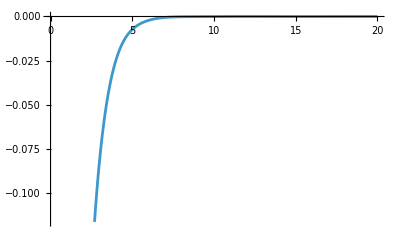

0.30396

```mathematica
(* RMS *)
n=1;
ϕr=Sum[v[[n,i]]*Rnlr[r,i,L],{i,1,Length[v]}]//Simplify
ϕr/.r->0 
Plot[ϕr,{r,0,20}]
rms=Sqrt[NIntegrate[ϕr^2*r^4,{r,0,Infinity}]];
rms/fm
```

```mathematica
(* SHO *)
Rnlp[p_,n_,l_,β_]:=((-1)^n*(-ⅈ)^l)/β^(3/2)*√((2*n!)/Gamma[n+l+3/2])*(p/β)^l ⅇ^(-p^2/(2*β^2))*LaguerreL[n,l+1/2,p^2/β^2]
Rnlr[r_,n_,l_,β_]:=β^(3/2)*√((2*n!)/Gamma[n+l+3/2])*(r*β)^l Exp[-(r^2*β^2)/2]*LaguerreL[n,l+1/2,r^2*β^2]
Solve[NIntegrate[ϕr^2*r^4,{r,0,Infinity}]==Integrate[Rnlr[r,n-1,L,β]^2*r^4,{r,0,Infinity}]&&β>0,β]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{β→0.795095}}